```mathematica
Quit[]
Exit[]
```

```mathematica
Get["/home/claire/policingdemography/policingdemography/policingdemography.wl"]
```

## Selection gradient and other useful functions of the model

```mathematica
sel=((1-m) (-1+m) n^4 rb^2 (n (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+Bb (-n (-1+p) y)^γ (-2+γ)) (C1 n y+2 C2 n y^2-n Pp y (p y)^η-Bb (-n (-1+p) y)^γ γ+n Pp (p y)^η η-n Pp y (p y)^η η))/((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^4 (1-((-1+m)^2 rb (Bb^2 rb th (-n (-1+p) y)^(2 γ)-2 Bb n rb th (-n (-1+p) y)^γ (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)+n^2 (rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η)^2+Bb (-n (-1+p) y)^γ (-1+γ))))/((n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2)))-(n^2 rb (C1 (-1-2 m (-1+n)+m^2 (-1+n)) n y+2 C2 (-1-2 m (-1+n)+m^2 (-1+n)) n y^2+n Pp y (p y)^η-2 m n Pp y (p y)^η+m^2 n Pp y (p y)^η+2 m n^2 Pp y (p y)^η-m^2 n^2 Pp y (p y)^η+Bb (-n (-1+p) y)^γ γ-n Pp (p y)^η η+n Pp y (p y)^η η))/((-1-2 m (-1+n)+m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))^2);
F[xm_,n_,nr_]:=(1-m)w[xm,xm,n]n+m nr;
w[x_,xn_,n_]:=re[x,xn,n]/(1+th re[x,xn,n]);
re[x_,xn_,n_]:=rb/n(1-(x C1+x^2 C2)+Bb((x+(n-1)xn)(1-p))^γ/n-Pp(1-x)((x+(n-1)xn)/n p)^η);
monopop={x->y,xn->y,xm->y,nr->n,r->(1-m)^2/(1+(1-(1-m)^2)(n-1)),r̄->1/n+(1-1/n)r};
```

```mathematica
sel/.{γ->1,η->1}//Simplify
```

(n rb (((C1+2 C1 m (-1+n)-C1 m^2 (-1+n)+Bb (-1+p)+p Pp+2 C2 y-4 C2 m y+2 C2 m^2 y+4 C2 m n y-2 C2 m^2 n y-2 p Pp y+2 m p Pp y-m^2 p Pp y-2 m n p Pp y+m^2 n p Pp y) (n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^2)/(-1-2 m (-1+n)+m^2 (-1+n))+((1-m) (-1+m) n rb (C1+Bb (-1+p)+p Pp+2 C2 y-2 p Pp y) (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))/((1+2 m (-1+n)-m^2 (-1+n)) (1-((-1+m)^2 rb^2 th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2)^2)/((n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^2)))))/(n-rb th (-1+C1 y+Bb (-1+p) y+p Pp y+C2 y^2-p Pp y^2))^4

## Explore parameters

```mathematica
pars={th->0.1,rb->20,c1->0,c2->0.1,b->2,d->0.3,p->0.5,eta->1,gamma->1,m->0.5};
```

Generate an error message

```mathematica
search[{{0.1},Range[1,3,2],{0},{0.1},{2},{0.3},{0.5},{1},{1}}]
```

search::len: You gave 9 parameters, this model needs 10

Launch a browse

```mathematica
saveTest=search[{{0.01},Range[1,50,5],{0},Range[0.1,6,0.5],Range[1,50,5],Range[0.5,10,2],Range[0.2,0.8,0.2],{2},{1},{0.5}}];
```

Power::infy: Infinite expression 1/0.^4 encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
If[StringQ[#],Print[#]]&/@saveTest[[2]]
```

```mathematica
collection={};
If[StringQ[#],AppendTo[collection,ToExpression[StringTake[#,19;;]]]]&/@saveTest[[2]];
collection
```

{}

```mathematica
Length[saveTest[[2]]]
```

24000

```mathematica
AnyTrue[#[["sZero"]]&/@saveTest[[2]],StringQ]
```

False

```mathematica
Solve[((1+2 m (-1+n)-m^2 (-1+n)) y (n^2+Bb rb th (-n (-1+p) y)^γ-n rb th (-1+C1 y+C2 y^2+Pp (p y)^η-Pp y (p y)^η))==0)/.{th->0.01,C1->0,η->1,γ->1,m->0.5,y->10^-10}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→-0.333333},{n→0.},{n→1.×10^-22 (-1.×10^20-1.×10^10 Bb+C2+1.×10^10 Bb p+1.×10^10 p Pp) rb}}

```mathematica
rbRange=Range[1,50,5];
c2Range=Range[0.1,6,0.5];
bRange=Range[1,50,5];
dRange=Range[0.5,10,2];
pRange=Range[0.2,0.8,0.2];
```

```mathematica
rbFixed=21;
c2Fixed=0.1;
bFixed=26;
dFixed=4.5;
pFixed=0.4;
```

```mathematica
rbFixedPos=Flatten[Position[saveTest[[1,All,2]],rbFixed]];
c2FixedPos=Flatten[Position[saveTest[[1,All,4]],c2Fixed]];
bFixedPos=Flatten[Position[saveTest[[1,All,5]],bFixed]];
dFixedPos=Flatten[Position[saveTest[[1,All,6]],dFixed]];
pFixedPos=Flatten[Position[saveTest[[1,All,7]],pFixed]];
```

#### Results for fixed parameters: th = 0.1, rb = 21, c1 = 0, d = 4.5, p = 0.4, η = 1, γ = 1, m = 0.5

Looking at the effect of c2 and b on s when y is near 0 and n is at the ecological equilibrium for y=1

```mathematica
linesOfInterest=Intersection[rbFixedPos,dFixedPos,pFixedPos];
```

```mathematica
resval=saveTest[[2,#,"sZero"]]&/@linesOfInterest;
c2val=saveTest[[1,#,4]]&/@linesOfInterest;
bval=saveTest[[1,#,5]]&/@linesOfInterest;
```

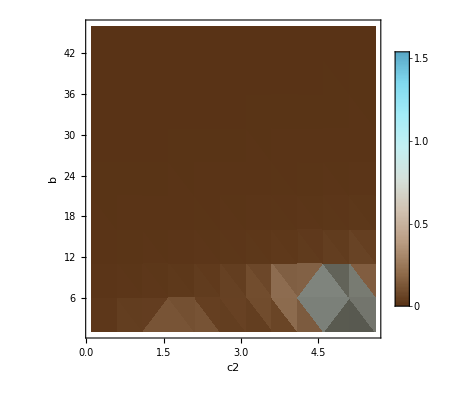

```mathematica
ListDensityPlot[{c2val[[#]],bval[[#]],resval[[#]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["BrownCyanTones"],FrameLabel->(Style[#,20]&/@{"c2","b","S(y≃0,n^*(y=1))"}),Frame->True]
```

effect on n at equilibrium when y is 1

```mathematica
resvalnOne=saveTest[[2,#,"nOne"]]&/@linesOfInterest;
```

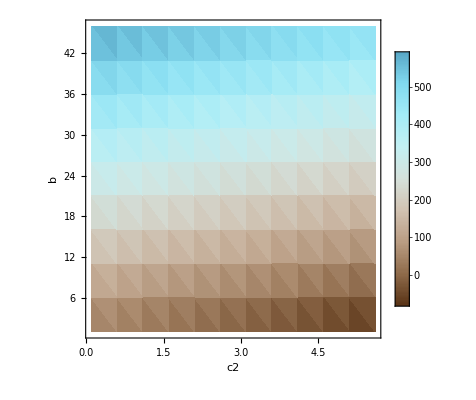

```mathematica
ListDensityPlot[{c2val[[#]],bval[[#]],resvalnOne[[#]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["BrownCyanTones"],FrameLabel->(Style[#,20]&/@{"c2","b","n^*(y=1)"}),Frame->True]
```

effect on n at equilibrium when y is 0

```mathematica
resvalnZero=saveTest[[2,#,"nZero"]]&/@linesOfInterest;
```

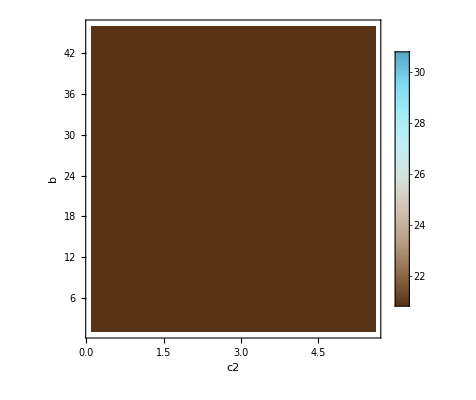

```mathematica
ListDensityPlot[{c2val[[#]],bval[[#]],resvalnZero[[#]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["BrownCyanTones"],FrameLabel->(Style[#,20]&/@{"c2","b","n^*(y=0)"}),Frame->True]
```

```mathematica
resvalsEqui0=saveTest[[2,#,"sEqui",1]]&/@linesOfInterest;
```

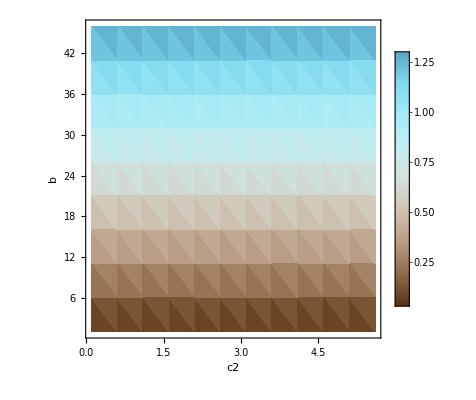

```mathematica
ListDensityPlot[{c2val[[#]],bval[[#]],resvalsEqui0[[#]]}&/@Range[Length[bval]],PlotLegends->Automatic,PlotRange->Full,ColorFunction->ColorData["BrownCyanTones"],FrameLabel->(Style[#,20]&/@{"c2","b","S(y≃0,n=n^*(y=0))"}),Frame->True]
```